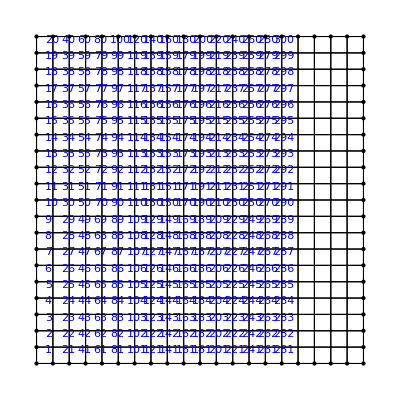

ElementMesh[{{0.,2.},{0.,2.}},{QuadElement[<400>]}]

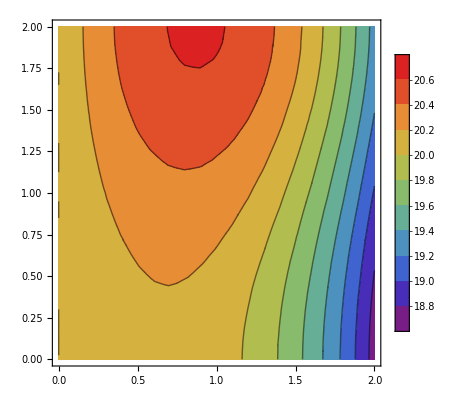

```mathematica
ClearAll["Global`*"];
Needs["NDSolve`FEM`"];
(*mesh size*)
h= 0.01;

mesh=ToElementMesh[Rectangle[{0,0},{2,2}],MeshOrder->1, MaxCellMeasure->h];
 
Show[mesh["Wireframe"["MeshElement"->"MeshElements","MeshElementIDStyle"->Blue,"ContinuousElementID"->True]],mesh["Wireframe"["MeshElement"->"PointElements","MeshElementIDStyle"->Red]]]
 

sol=NDSolveValue[{2D[u[x,y],x,x]+2D[u[x,y],y,y]+2x+y^2==NeumannValue[5.0,x==2&&0≤y≤2],DirichletCondition[u[x,y]==20,x==0&&0≤y≤2]},u,{x,y}∈mesh];

sol["ElementMesh"]
ContourPlot[sol[x,y],{x,y}∈mesh,Mesh->None,ColorFunction->"Rainbow",BaseStyle->{FontWeight->"Normal",FontSize->18},PlotRange->All,PlotLegends->BarLegend[Automatic,LabelStyle->{Black,FontFamily->"Times New Roman",FontSize->18}],LabelStyle->Directive[Black,FontFamily->"Times New Roman"]]
```